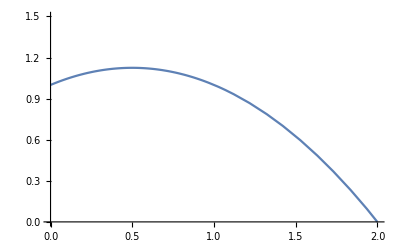

```mathematica
Plot[(1+x)*(1- (x/2)^(1)), {x,0,5}, PlotRange->{{0, 2},{0, 1.5}}]
```

```mathematica
x/(1+x)
```

x/(1+x)

```mathematica
D[x/(1+x), x]
```

-x/(1+x)^2+1/(1+x)

```mathematica
(1+x)(1- (x/c)^θ)
```

(1+x) (1-(x/c)^θ)

```mathematica
Expand[(1+x) (1-(x/c)^θ)]
```

1+x-(x/c)^θ-x (x/c)^θ

```mathematica
D[((1+x) (1-(x/c)^θ)), x]
```

1-(x/c)^θ-((x/c)^(-1+θ) (1+x) θ)/c

```mathematica
gp[x_]:=1-(x/c)^θ-((x/c)^(-1+θ) (1+x) θ)/c
```

```mathematica
gp[ α / (1-α)]
```

1-(α/(c (1-α)))^θ-((α/(c (1-α)))^(-1+θ) (1+α/(1-α)) θ)/c

```mathematica
Simplify[1-(α/(c (1-α)))^θ-((α/(c (1-α)))^(-1+θ) (1+α/(1-α)) θ)/c]
```

1-(α/(c-c α))^θ-((α/(c-c α))^θ θ)/α

```mathematica
Simplify[1-(x/c)^θ-((x/c)^(-1+θ) (1+x) θ)/c]
```

1-(x/c)^θ-((x/c)^θ (1+x) θ)/x

Reduce[1-(x/c)^θ-((x/c)^θ (1+x) θ)/x>0,x]

```mathematica
Integrate[(x^2)*Sin[(n*Pi*x)], {x,0,1}]
```

(-2+(2-n^2 π^2) Cos[n π]+2 n π Sin[n π])/(n^3 π^3)

```mathematica
(-2+(2-n^2 π^2) Cos[n π])/(n^3 π^3)
```

(-2+(2-n^2 π^2) Cos[n π])/(n^3 π^3)

```mathematica
Integrate[x*Sin[n*Pi*x], {x,0,1}]
```

(-n π Cos[n π]+Sin[n π])/(n^2 π^2)